```mathematica
Δ[q_]:=(q + q^-1) / 2;
```

```mathematica
s = NSolve[q ^(2 * 50)==1, q][[All,1,2]];
```

```mathematica
Re[Δ /@ s]
```

{-1.,-0.998027,-0.998027,-0.992115,-0.992115,-0.982287,-0.982287,-0.968583,-0.968583,-0.951057,-0.951057,-0.929776,-0.929776,-0.904827,-0.904827,-0.876307,-0.876307,-0.844328,-0.844328,-0.809017,-0.809017,-0.770513,-0.770513,-0.728969,-0.728969,-0.684547,-0.684547,-0.637424,-0.637424,-0.587785,-0.587785,-0.535827,-0.535827,-0.481754,-0.481754,-0.425779,-0.425779,-0.368125,-0.368125,-0.309017,-0.309017,-0.24869,-0.24869,-0.187381,-0.187381,-0.125333,-0.125333,-0.0627905,-0.0627905,0.,0.,0.0627905,0.0627905,0.125333,0.125333,0.187381,0.187381,0.24869,0.24869,0.309017,0.309017,0.368125,0.368125,0.425779,0.425779,0.481754,0.481754,0.535827,0.535827,0.587785,0.587785,0.637424,0.637424,0.684547,0.684547,0.728969,0.728969,0.770513,0.770513,0.809017,0.809017,0.844328,0.844328,0.876307,0.876307,0.904827,0.904827,0.929776,0.929776,0.951057,0.951057,0.968583,0.968583,0.982287,0.982287,0.992115,0.992115,0.998027,0.998027,1.}

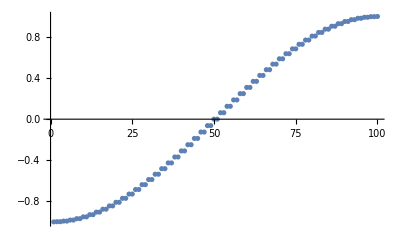

```mathematica
ListPlot[Re[Δ /@ s]]
```